# Map, Apply and colleagues

```mathematica
Needs["brosvisuals`"]
```

## Map (/@)

Map[] applies a command given as first argument to every expression given as second argument. An optional third argument specifies the level at which Map[] operates. The default level is {1}.

```mathematica
Map[f,{1,2,3,4}]
```

{f[1],f[2],f[3],f[4]}

this is the same (short syntax):

```mathematica
f/@{1,2,3,4}
```

{f[1],f[2],f[3],f[4]}

with third argument:

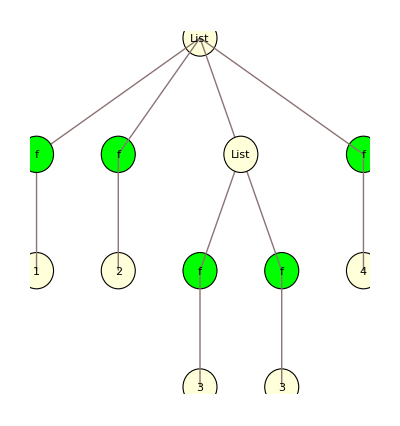

```mathematica
mySimpleTreeFormRenderer[Map[f,{1,2,{3,3},4},{-1}],{f},Green]
```

with three level deep list:

```mathematica
Map[f,{1,2,{lev2,lev2,{lev3,lev3}},4},{2}]
```

{1,2,{f[lev2],f[lev2],f[{lev3,lev3}]},4}

```mathematica
Map[f,{1,2,{lev2,lev2,{lev3,lev3}},4},{3}]
```

{1,2,{lev2,lev2,{f[lev3],f[lev3]}},4}

```mathematica
Map[f,{1,2,{lev2,lev2,{lev3,lev3}},4},{2,3}]
```

{1,2,{f[lev2],f[lev2],f[{f[lev3],f[lev3]}]},4}

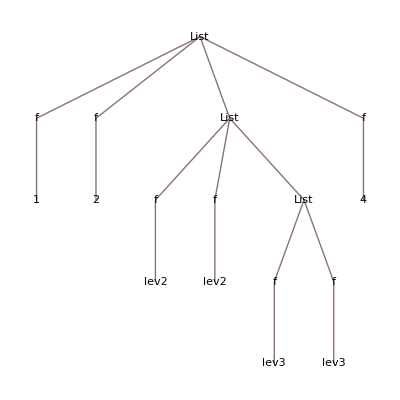

```mathematica
Map[f,{1,2,{lev2,lev2,{lev3,lev3}},4},{-1}]//TreeForm
```

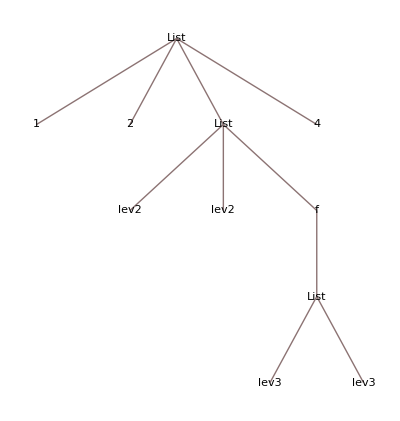

```mathematica
Map[f,{1,2,{lev2,lev2,{lev3,lev3}},4},{-2}]//TreeForm
```